# Data science and Machine Learning II - Green Bonds Project

## Data import

### Local Directory

```mathematica
localdir = "C:\\Users\\massi\\Documents\\Università\\MASTER_EPFL\\Semester_3\\machine Learning\\Local_Green_Bonds\\files";
localreportsPath =FileNameJoin[{localdir,""}];
localfoldersPath = FileNames[All,localreportsPath];
localpdfPath = Map[FileNames[All,#]&,localfoldersPath];
localfileMaxNumber = Map[Length,localpdfPath]//Min;
SeedRandom[1234];
randomSample = Map[RandomSample[#,localfileMaxNumber]&,localpdfPath];
Map[Length,randomSample]
```

{78,78,78,78}

### Github Directory

```mathematica
dir = NotebookDirectory[];
reportsPath =FileNameJoin[{dir,"training_reports"}];
foldersPath = FileNames[All,reportsPath];
pdfPath = Map[FileNames[All,#]&,foldersPath];
```

```mathematica
(* the line below substitute the repository directory with the local directory to use more PDFs*)
pdfPath = randomSample;
```

```mathematica
fileMaxNumber = Length[pdfPath[[1]]]
labelsList = {"green","social", "sustainability","sustainability related"};
pdfClassification = AssociationThread[labelsList->pdfPath];
```

78

### Text Extraction

```mathematica
ImportPlainText[label_,textNumber_]:=ToString[Import[pdfClassification[label][[textNumber]], "Plaintext"],CharacterEncoding->"ASCII"];
```

```mathematica
pdfGreen = ImportPlainText["green",1];
pdfSocial = ImportPlainText["social",1];
```

```mathematica
DivideTextWords[pdfPlaintex_]:= WordStem[DeleteStopwords[ToLowerCase[TextWords[pdfPlaintex]]]];
CleanText[wordList_] :=DeleteCases[wordList,_?(StringContainsQ[#,{"https","www",".com","@","☐","%","..","©", "☒", "+" ,"ii"}]&)];
ManageText[label_,textNumber_]:=Dataset[{<|"text"->CleanText[DivideTextWords[ImportPlainText[label,textNumber]]], "label"-> label|>}]
```

```mathematica
(* Takes more or less 5minutes *)
```

```mathematica
LabeledDataset =ManageText["green",1] ;
For[textNumber=1,textNumber<fileMaxNumber+1,textNumber++,For[label =1,label<5,label++,LabeledDataset=Join[LabeledDataset, ManageText[labelsList[[label]],textNumber]]]]
LabeledDataset = LabeledDataset[2;;All];
```

## Machine Learning

### Data split

```mathematica
{nobs, ncol} = Dimensions[LabeledDataset];
{trainingSet,testSet}=TakeDrop[RandomSample[LabeledDataset],Floor[nobs*0.8]];

totalCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[LabeledDataset,"label"]]],"label"];
trainingCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[trainingSet,"label"]]],"label"];
testCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[testSet,"label"]]],"label"];
```

```mathematica
totalChart = BarChart[ Normal @ totalCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Total dataset"];
```

```mathematica
trainingChart =BarChart[ Normal @ trainingCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Training dataset"];
```

```mathematica
testChart =BarChart[ Normal @ testCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Test dataset"];
```

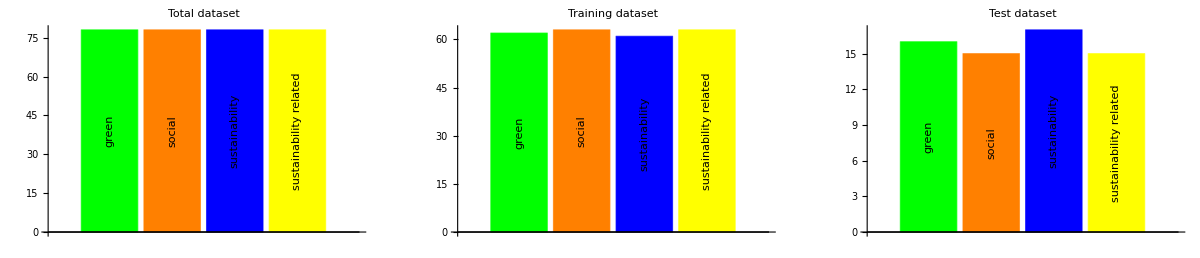

```mathematica
GraphicsRow[{totalChart, trainingChart, testChart}, ImageSize->Full]
```

### Logistic Regression

```mathematica
cLog=Classify[trainingSet->"label",Method->"LogisticRegression",ValidationSet->Automatic];
cLogMeasurementsTest = ClassifierMeasurements[cLog, testSet];
```

### K-nearest Neighbors

```mathematica
cKNN =Classify[trainingSet -> "label", Method -> {"NearestNeighbors", "NeighborsNumber" -> #},ValidationSet->Automatic] & /@ Range[10];
cKNNMeasurements = ClassifierMeasurements[#, trainingSet] & /@ cKNN;
keyOpt = Keys[Sort[<|#->cKNNMeasurements[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cKNNMeasurementsTest = ClassifierMeasurements[#, testSet] & /@ cKNN;
keyOptTest = Keys[Sort[<|#->cKNNMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cKNNAccTest=cKNNMeasurementsTest[[keyOptTest]];
cKNNBest = cKNN[[keyOptTest]];
```

### Decision Tree

```mathematica
cTree=Classify[trainingSet-> "label", Method -> {"DecisionTree", "FeatureFraction" -> #}]&/@ (Range[10]/(ncol-1));
cTreeMeasurements = ClassifierMeasurements[#, trainingSet] & /@ cTree;
keyOptTree = Keys[Sort[<|#->cTreeMeasurements[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cTreeMeasurementsTest = ClassifierMeasurements[#, testSet] & /@ cTree;
keyOptTestTree = Keys[Sort[<|#->cTreeMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cTreeBest = cTree[[keyOptTestTree]];
cTreeAccTestBest = ClassifierMeasurements[cTreeBest, testSet];
```

### Random Forest

```mathematica
cRandFor=Classify[trainingSet->"label",Method->"RandomForest",ValidationSet->Automatic];
cRandForMeasurements = ClassifierMeasurements[cRandFor, trainingSet];
cRandForMeasurementsTest = ClassifierMeasurements[cRandFor, testSet];
```

### Markov

```mathematica
cMarkov=Classify[trainingSet->"label",Method->"Markov",ValidationSet->Automatic];
cMarkovMeasurements = ClassifierMeasurements[cMarkov, trainingSet];
cMarkovMeasurementsTest = ClassifierMeasurements[cMarkov, testSet];
```

### Neural Network

```mathematica
cNN=Classify[trainingSet->"label",Method->"NeuralNetwork",ValidationSet->Automatic];
cNNMeasurements = ClassifierMeasurements[cNN, trainingSet];
cNNMeasurementsTest = ClassifierMeasurements[cNN, testSet];
```

### Results

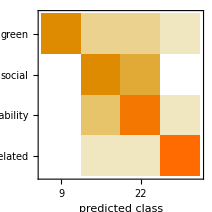
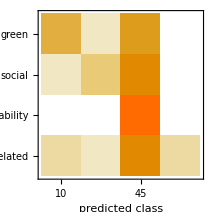
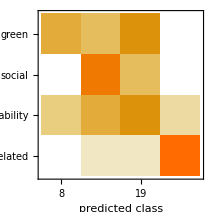
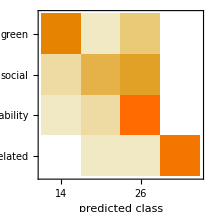
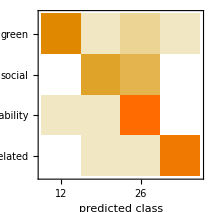
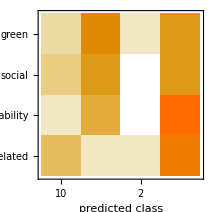
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (68.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 0.42 ± 0.036
Mean cross entropy | 0.866 ± 0.085
Single evaluation time | 43.9 ms/example
Batch evaluation speed | 68. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (48.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 0.271 ± 0.029
Mean cross entropy | 1.3 ± 0.11
Single evaluation time | 49.5 ms/example
Batch evaluation speed | 69.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (57.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 0.344 ± 0.036
Mean cross entropy | 1.07 ± 0.1
Single evaluation time | 52.4 ms/example
Batch evaluation speed | 52.6 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (70.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 0.402 ± 0.03
Mean cross entropy | 0.91 ± 0.075
Single evaluation time | 53.7 ms/example
Batch evaluation speed | 66.2 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (75.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 4.06×10^-62 ± 2.7×10^-41
Mean cross entropy | 141. ± 49.
Single evaluation time | 55. ms/example
Batch evaluation speed | 26.2 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 63
Accuracy | (27.6.) %
Accuracy baseline | (27.6.) %
Geometric mean of probabilities | 0.251 ± 0.00096
Mean cross entropy | 1.38 ± 0.0038
Single evaluation time | 72.7 ms/example
Batch evaluation speed | 21.4 examples/s
-Graphics- | }

```mathematica
{cLogMeasurementsTest, cKNNAccTest, cTreeAccTestBest, cRandForMeasurementsTest , cMarkovMeasurementsTest, cNNMeasurementsTest}
```

## Optimization

#### Sentences Model

We try by keeping the entire sentences to preserve the meaning.

```mathematica
DivideTextSentence[pdfPlaintex_]:= WordStem[DeleteStopwords[ToLowerCase[TextSentences[pdfPlaintex]]]];
CleanTextSentence[wordList_] :=DeleteCases[wordList,_?(StringContainsQ[#,{"https","www",".com","@"}]&)];
ManageTextSentence[label_,textNumber_]:=Dataset[{<|"text"->CleanTextSentence[DivideTextSentence[ImportPlainText[label,textNumber]]], "label"-> label|>}]
```

```mathematica
LabeledDatasetSentence =ManageTextSentence["green",1] ;
For[textNumber=1,textNumber<fileMaxNumber+1,textNumber++,For[label =1,label<5,label++,LabeledDatasetSentence=Join[LabeledDatasetSentence, ManageTextSentence[labelsList[[label]],textNumber]]]]
LabeledDatasetSentence = LabeledDatasetSentence[2;;All];
```

```mathematica
{nobsS, ncolS} = Dimensions[LabeledDatasetSentence];
{trainingSetSentence,testSetSentence}=TakeDrop[RandomSample[LabeledDatasetSentence],Floor[nobsS*0.8]];
```

### Logistic Regression

```mathematica
cLogSentence=Classify[trainingSetSentence->"label",Method->"LogisticRegression",ValidationSet->Automatic];
cLogMeasurementsTestSentence = ClassifierMeasurements[cLogSentence, testSetSentence];
```

### K-nearest Neighbors

```mathematica
cKNNSentence =Classify[trainingSetSentence -> "label", Method -> {"NearestNeighbors", "NeighborsNumber" -> #},ValidationSet->Automatic] & /@ Range[10];
cKNNMeasurementsSentence = ClassifierMeasurements[#, trainingSetSentence] & /@ cKNNSentence;
keyOptS = Keys[Sort[<|#->cKNNMeasurementsSentence[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cKNNMeasurementsTestSentence = ClassifierMeasurements[#, testSetSentence] & /@ cKNNSentence;
keyOptTestS = Keys[Sort[<|#->cKNNMeasurementsTestSentence[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cKNNAccTestS=cKNNMeasurementsTestSentence[[keyOptTestS]];
cKNNBestS = cKNN[[keyOptTestS]];
```

### Decision Tree

```mathematica
cTreeS=Classify[trainingSetSentence-> "label", Method -> {"DecisionTree", "FeatureFraction" -> #}]&/@ (Range[10]/(ncolS-1));
cTreeMeasurementsS = ClassifierMeasurements[#, trainingSetSentence] & /@ cTreeS;
keyOptTreeS = Keys[Sort[<|#->cTreeMeasurementsS[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cTreeMeasurementsTestS = ClassifierMeasurements[#, testSetSentence] & /@ cTreeS;
keyOptTestTreeS = Keys[Sort[<|#->cTreeMeasurementsTestS[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cTreeBestS = cTreeS[[keyOptTestTreeS]];
cTreeAccTestBestS = ClassifierMeasurements[cTreeBestS, testSetSentence];
```

### Random Forest

```mathematica
cRandForS=Classify[trainingSetSentence->"label",Method->"RandomForest",ValidationSet->Automatic];
cRandForMeasurementsS = ClassifierMeasurements[cRandForS, trainingSetSentence];
cRandForMeasurementsTestS = ClassifierMeasurements[cRandForS, testSetSentence];
```

### Markov

```mathematica
cMarkovS=Classify[trainingSetSentence->"label",Method->"Markov",ValidationSet->Automatic];
cMarkovMeasurementsS = ClassifierMeasurements[cMarkovS, trainingSetSentence];
cMarkovMeasurementsTestS = ClassifierMeasurements[cMarkovS, testSetSentence];
```

### Neural Network

```mathematica
cNNs=Classify[trainingSetSentence->"label",Method->"NeuralNetwork",ValidationSet->Automatic];
cNNMeasurementsS = ClassifierMeasurements[cNNS, trainingSetSentence];
cNNMeasurementsTestS = ClassifierMeasurements[cNNS, testSetSentence];
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of cNNS.

### Results

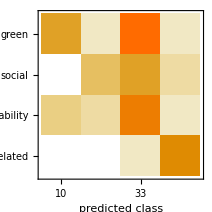
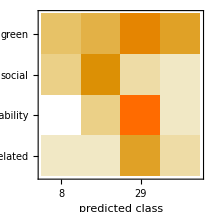
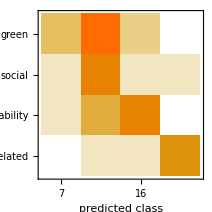
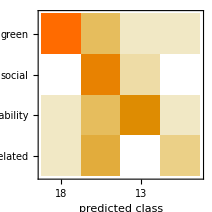
{cLogMeasurementsTestS,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (49.6.) %
Accuracy baseline | (37.6.) %
Geometric mean of probabilities | 0.24 ± 0.034
Mean cross entropy | 1.43 ± 0.14
Single evaluation time | 17.8 ms/example
Batch evaluation speed | 574. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (41.6.) %
Accuracy baseline | (37.6.) %
Geometric mean of probabilities | 0.276 ± 0.012
Mean cross entropy | 1.29 ± 0.042
Single evaluation time | 19.7 ms/example
Batch evaluation speed | 552. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (52.6.) %
Accuracy baseline | (37.6.) %
Geometric mean of probabilities | 0.316 ± 0.019
Mean cross entropy | 1.15 ± 0.062
Single evaluation time | 22.4 ms/example
Batch evaluation speed | 432. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (63.6.) %
Accuracy baseline | (37.6.) %
Geometric mean of probabilities | 1.8×10^-9 ± 3.7×10^-7
Mean cross entropy | 20.1 ± 6.
Single evaluation time | 5.15 ms/example
Batch evaluation speed | 409. examples/s
-Graphics- | ,ClassifierMeasurements[cNNS,Dataset[<>]]}

```mathematica
{cLogMeasurementsTestS, cKNNAccTestS, cTreeAccTestBestS, cRandForMeasurementsTestS, cMarkovMeasurementsTestS, cNNMeasurementsTestS}
```

#### NetModel

```mathematica
LowerCaseStopwords[pdfPlaintex_]:= DeleteStopwords[ToLowerCase[pdfPlaintex]];
CleanSentenceNet[wordList_] :=DeleteCases[wordList,_?(StringContainsQ[#,{"https","www",".com","@"}]&)];
ManageTextNet[label_,textNumber_]:=Dataset[{<|"text"->netEPEmb[CleanSentenceNet[DeleteStopwords[ImportPlainText[label,textNumber]]]], "label"-> label|>}];

netBERT = NetModel["BERT Trained on BookCorpus and Wikipedia Data"];
netEPEmb = NetModel[{"BPEmb Subword Embeddings Trained on Wikipedia","Language"->"English","VocabularySize"->5000,"Dimensions"->25}];
```

```mathematica
x = Dataset[{<|"text"->netEPEmb[DeleteStopwords[ImportPlainText["green", 1]]], "label"-> "green"|>}];
y = Dataset[{<|"text"->netEPEmb[DeleteStopwords[ImportPlainText["social", 1]]], "label"-> "social"|>}];
xy = Join[x,y];
```

```mathematica
cMarkovNet=Classify[xy->"label",Method->"LogisticRegression",ValidationSet->Automatic]
```

ClassifierFunction[…]

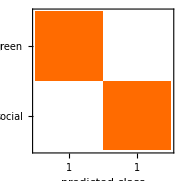
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 2
Accuracy | (100.00000000000000022) %
Accuracy baseline | (50.50.) %
Single evaluation time | 330. ms/example
Batch evaluation speed | 0.593 examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[cMarkovNet, xy]
```

```mathematica
LabeledDatasetNetSentence = ManageTextNet["green", 1];
For[textNumber=1,textNumber<fileMaxNumber+1,textNumber++,Print[textNumber];For[label =1,label<5,label++,LabeledDatasetNetSentence=Join[LabeledDatasetNetSentence, ManageTextNet[labelsList[[label]],textNumber]]]]
LabeledDatasetNetSentence= LabeledDatasetNetSentence[2;;,All];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

```mathematica
{nobsNet, ncolNet} = Dimensions[LabeledDatasetNetSentence];
{trainingSetNet,testSetNet}=TakeDrop[RandomSample[LabeledDatasetNetSentence],Floor[nobsNet*0.8]];
```

#### Markov

```mathematica
cMarkovNet=Classify[trainingSetNet->"label",Method->"Markov",ValidationSet->Automatic]
cMarkovMeasurementsNet = ClassifierMeasurements[cMarkovNet, trainingSetNet];
```

ClassifierFunction[…]

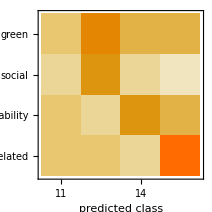
Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (41.6.) %
Accuracy baseline | (30.6.) %
Geometric mean of probabilities | 2.97×10^-51 ± 5.8×10^-42
Mean cross entropy | 116. ± 22.
Single evaluation time | 4.03 s/example
Batch evaluation speed | 15.8 examples/min
-Graphics- |

```mathematica
cMarkovMeasurementsTestNet = ClassifierMeasurements[cMarkovNet, testSetNet]
```

#### Logistic

```mathematica
cLogNet=Classify[trainingSetNet->"label",Method->"LogisticRegression",ValidationSet->Automatic]
cLogNet = ClassifierMeasurements[cLogNet, trainingSetNet];
```

$Aborted

Set::partd: Part specification MachineLearning`file16Decision`PackagePrivate`paramutility$14019879⟦All,1⟧ is longer than depth of object.

Set::write: Tag String in Model[Utility] is Protected.

Set::write: Tag String in Model[TieBreaker] is Protected.

ArrayPad::arr: First argument «551742056 bytes»[LogProbabilities] to ArrayPad should be an array.

Part::pspec1: Part specification Model is not applicable.

Part::pspec1: Part specification Predictions is not applicable.

Part::pspec1: Part specification TestSet is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

MapThread::mptd: Object «551742056 bytes»⟦Predictions,{1}⟧ at position {2, 1} in MapThread[SameQ,{«551742056 bytes»⟦Predictions,{1}⟧,«551742056 bytes»⟦TestSet,Output,{1}⟧}] has only 0 of required 1 dimensions.

Commonest::arg1: The first argument is expected to be a list.

MapThread::mptd: Object «551742056 bytes»[LogProbabilities] at position {2, 1} in MapThread[Part,{«551742056 bytes»[LogProbabilities],0}] has only 0 of required 1 dimensions.

MapThread::mptd: Object «551742056 bytes»[LogProbabilities] at position {2, 1} in MapThread[Part,{«551742056 bytes»[LogProbabilities],0.}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Function::slotn: Slot number 2 in {Take[#1,Ceiling[3]],#2}& cannot be filled from ({Take[#1,Ceiling[3]],#2}&)[1./((31536000 IntegerPart[Power[«2»] Power[«2»] Power[«2»]])/(86400 10^3)+Round[31536000 Power[«2»] FractionalPart[«1»]]/10^3)].

Take::take: Cannot take positions 1 through 3 in 1./((31536000 IntegerPart[10^3/(31536000 «2»)])/(86400 10^3)+Round[(31536000 FractionalPart[Times[«3»]])/86400]/10^3).

Take::take: Cannot take positions 1 through 3 in 1./(0.365 IntegerPart[0.0000317098/Times[«2»]]+0.001 Round[365. FractionalPart[Times[«2»]]]).

Part::partd: Part specification «551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧ is longer than depth of object.

Part::partd: Part specification «551742056 bytes»[CountMatrix]⟦{1,2},-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through -2 in CountMatrix.

Part::pkspec1: The expression If[Total[All]>0.,All/Total[All],All] cannot be used as a part specification.

Part::take: Cannot take positions 1 through -2 in CountMatrix.

Part::partw: Part {1,2} of Transpose[Transpose[If[Total[«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧]>0.,«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧/Total[««1»»[«1»]⟦All,Span[«2»]⟧],«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧]]] does not exist.

Part::pkspec1: The expression ExtendedClasses cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1,2},«551742056 bytes»⟦ExtendedClasses⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,2},Total[«551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧]} cannot be transposed.

Part::partw: Part 3 of Total[«551742056 bytes»[CountMatrix]] does not exist.

Transpose::nmtx: The first two levels of {{1,2},«551742056 bytes»⟦ExtendedClasses⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in actual <>«551742056 bytes»⟦Model,1,Output,Name⟧.

StringJoin::string: String expected at position 2 in predicted <>«551742056 bytes»⟦Model,1,Output,Name⟧.

Part::partw: Part 2 of «551742056 bytes»[CountMatrix] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

MatrixPlot::mat0: Argument «551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧ at position 1 is not a matrix.

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Deploy[Framed[Column[{Item[Framed[Classifier Measurements, <<2>>], <<4>>, Frame -> {<<2>>}], <<1>>}, <<5>>], <<4>>]].

Set::partd: Part specification MachineLearning`file16Decision`PackagePrivate`paramutility$12893913⟦All,1⟧ is longer than depth of object.

Set::write: Tag String in Model[Utility] is Protected.

Set::write: Tag String in Model[TieBreaker] is Protected.

ArrayPad::arr: First argument «551742056 bytes»[LogProbabilities] to ArrayPad should be an array.

Part::pspec1: Part specification Model is not applicable.

Part::pspec1: Part specification Predictions is not applicable.

Part::pspec1: Part specification TestSet is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

MapThread::mptd: Object «551742056 bytes»⟦Predictions,{1}⟧ at position {2, 1} in MapThread[SameQ,{«551742056 bytes»⟦Predictions,{1}⟧,«551742056 bytes»⟦TestSet,Output,{1}⟧}] has only 0 of required 1 dimensions.

Commonest::arg1: The first argument is expected to be a list.

MapThread::mptd: Object «551742056 bytes»[LogProbabilities] at position {2, 1} in MapThread[Part,{«551742056 bytes»[LogProbabilities],0}] has only 0 of required 1 dimensions.

MapThread::mptd: Object «551742056 bytes»[LogProbabilities] at position {2, 1} in MapThread[Part,{«551742056 bytes»[LogProbabilities],0.}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Function::slotn: Slot number 2 in {Take[#1,Ceiling[3]],#2}& cannot be filled from ({Take[#1,Ceiling[3]],#2}&)[1./((31536000 IntegerPart[Power[«2»] Power[«2»] Power[«2»]])/(86400 10^3)+Round[31536000 Power[«2»] FractionalPart[«1»]]/10^3)].

Take::take: Cannot take positions 1 through 3 in 1./((31536000 IntegerPart[10^3/(31536000 «2»)])/(86400 10^3)+Round[(31536000 FractionalPart[Times[«3»]])/86400]/10^3).

Take::take: Cannot take positions 1 through 3 in 1./(0.365 IntegerPart[0.0000317098/Times[«2»]]+0.001 Round[365. FractionalPart[Times[«2»]]]).

Part::partd: Part specification «551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧ is longer than depth of object.

Part::partd: Part specification «551742056 bytes»[CountMatrix]⟦{1,2},-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through -2 in CountMatrix.

Part::pkspec1: The expression If[Total[All]>0.,All/Total[All],All] cannot be used as a part specification.

Part::take: Cannot take positions 1 through -2 in CountMatrix.

Part::partw: Part {1,2} of Transpose[Transpose[If[Total[«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧]>0.,«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧/Total[««1»»[«1»]⟦All,Span[«2»]⟧],«551742056 bytes»[CountMatrix]⟦All,1;;-2⟧]]] does not exist.

Part::pkspec1: The expression ExtendedClasses cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1,2},«551742056 bytes»⟦ExtendedClasses⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,2},Total[«551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧]} cannot be transposed.

Part::partw: Part 3 of Total[«551742056 bytes»[CountMatrix]] does not exist.

Transpose::nmtx: The first two levels of {{1,2},«551742056 bytes»⟦ExtendedClasses⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in actual <>«551742056 bytes»⟦Model,1,Output,Name⟧.

StringJoin::string: String expected at position 2 in predicted <>«551742056 bytes»⟦Model,1,Output,Name⟧.

Part::partw: Part 2 of «551742056 bytes»[CountMatrix] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

MatrixPlot::mat0: Argument «551742056 bytes»[CountMatrix]⟦{1,2},{1,2}⟧ at position 1 is not a matrix.

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Deploy[Framed[Column[{Item[Framed[Classifier Measurements, <<2>>], <<4>>, Frame -> {<<2>>}], <<1>>}, <<5>>], <<4>>]].

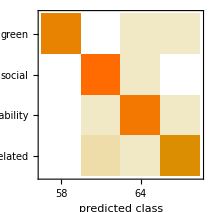
ClassifierMeasurements[Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 249
Accuracy | (96.81.1) %
Accuracy baseline | (26.92.8) %
Geometric mean of probabilities | 0.858 ± 0.027
Mean cross entropy | 0.153 ± 0.032
Single evaluation time | 1.32 s/example
Batch evaluation speed | 0.31 examples/s
-Graphics- | ,Dataset[<>]]

```mathematica
cLogMeasurementsTestNet = ClassifierMeasurements[cLogNet, testSetNet]
```